```mathematica
FindBoundedLine[slope_,intercept_, boundary_]:=Module[{
generatedLine,
interceptionWithY0,
interceptionWithX0,
interceptionWithRightBoundary,
interceptionWithTopBoundary,
contacts
},
generatedLine[x_]:= slope x + intercept;
interceptionWithY0 = generatedLine[0];
interceptionWithX0 = -intercept / slope;
interceptionWithRightBoundary = generatedLine[boundary];
interceptionWithTopBoundary = (boundary - intercept)/slope;

interceptionWithY0 = If[boundary >=interceptionWithY0 >= 0 , interceptionWithY0, Null];
interceptionWithX0 = If[boundary >=interceptionWithX0 >= 0,interceptionWithX0, Null]; 
interceptionWithRightBoundary = If[boundary >= interceptionWithRightBoundary >=0,interceptionWithRightBoundary,Null];
interceptionWithTopBoundary = If[boundary >= interceptionWithTopBoundary >=0, interceptionWithTopBoundary,Null];

contacts =DeleteDuplicates[Select[ {{0,interceptionWithY0},{ interceptionWithX0,0}, {boundary,interceptionWithRightBoundary}, {interceptionWithTopBoundary,boundary}},FreeQ[#,Null]&]
]]
```

```mathematica
SpaceTime[observers_,events_,boxLength_,backgroundResolution_,opacityOfBackgroundLines_] := Module[{
imageObjects,
bl,
backgroundLines,
mainLine,
evs,
obs,
contacts,
cones
},
bl = boxLength; 
backgroundLines = Table[
{
Opacity[opacityOfBackgroundLines],
Line[{{0,backgroundResolution i},{bl -backgroundResolution i,bl}}],Line[{{backgroundResolution i,0},{bl,bl-backgroundResolution i}}]
}, {i,1,(bl-1)/backgroundResolution}
];
backgroundLines = Join[
backgroundLines,{
Opacity[opacityOfBackgroundLines],
 Line[{{0,0},{bl,bl}}]
}];
backgroundLines = Join[backgroundLines,Table[
{
Opacity[opacityOfBackgroundLines],
Line[{{bl,backgroundResolution i},{backgroundResolution i,bl}}],Line[{{bl - backgroundResolution i, 0},{0,bl -  backgroundResolution i}}]
}, {i,1,(bl-1)/backgroundResolution}
]];
backgroundLines = Join[backgroundLines, {
Opacity[opacityOfBackgroundLines],
 Line[{{bl,0},{0,bl}}]
}];

(*Event Cones and Points *)
evs = Table[{Opacity[1.0],Point[{events[[i]][[1]],events[[i]][[2]]}]},{i,1,Length[events]}];
contacts= Table[{events[[i]],FindBoundedLine[1,events[[i]][[2]] -events[[i]][[1]],bl],FindBoundedLine[-1,events[[i]][[2]]+events[[i]][[1]],bl]},{i,1,Length[events]}];
cones = Table[{
Orange,
Line[{contacts[[i]][[1]],contacts[[i]][[2]][[1]]}],
Line[{contacts[[i]][[1]],contacts[[i]][[2]][[2]]}],
Line[{contacts[[i]][[1]],contacts[[i]][[3]][[1]]}],
Line[{contacts[[i]][[1]],contacts[[i]][[3]][[2]]}]
},{i,1,Length[contacts]}];


imageObjects = cones;
imageObjects = Join[imageObjects,backgroundLines,evs,
(*observers*)
{Red,Opacity[1.0],Line[{{0.3,0},{0.3,bl}}]},
{Purple,Opacity[1.0],Line[{{2.7,0},{2.7,bl}}]},
{Purple,Opacity[1.0],Line[{{3.3,0},{3.3,bl}}]}
];
Graphics[imageObjects] 
]
```

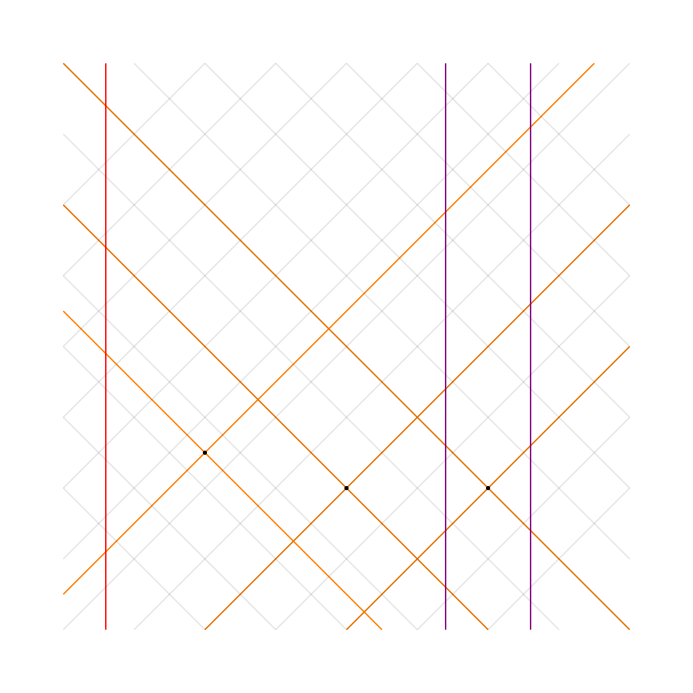

```mathematica
x = SpaceTime[{
1,0.25
},{
{1,1.25},
{2,1},
{3,1}
},4,0.5,0.1]
```

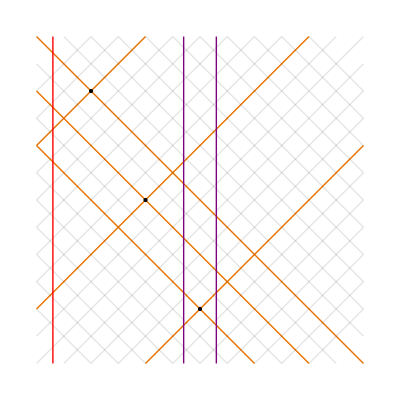

```mathematica
(*Event and observer data*)x=SpaceTime[{1,0.25},{
{1,5},(*Event A at x=1,t=1*)
{2,3},(*Event B at x=3,t=2*)
{3,1} (*Event C at x=3,t=1.5*)
},6,0.5,0.1]
```

```mathematica
ABC,BAC,BCA,CBA
```